D:\Development\Math in Chemistry\Assignment2 1D_Quantum_Systems\Morse

8

120

0.185001 (1-ⅇ^(-1.21023 (-1.77993+x)))^2

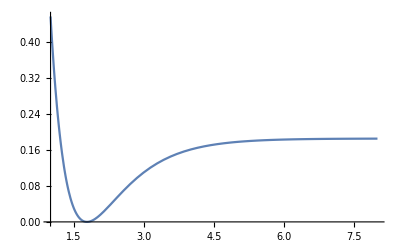

```mathematica
SetDirectory[NotebookDirectory[]]
L=6
Nt=120

potentialFun[x_]=0.001593601*116.09*(1-Exp[-2.287*0.5291772108*(x-0.9419/0.5291772108)])^2
Plot[potentialFun[x],{x,1,L}]
```

```mathematica
12
```

12

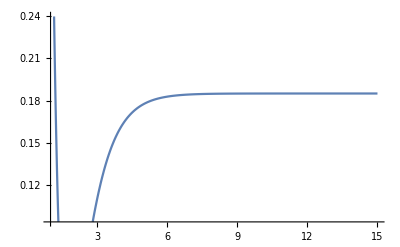

-Graphics-

```mathematica
sinBasis=Table[Sqrt[2/L]Sin[π i (x)/L],{i,Nt}]
kineticEnerOperator[f_,x_]:=(-D[f,{x,2}])/(2*1728.16)
harmonicOperator[f_,x_]:=kineticEnerOperator[f,x]+potentialFun[x]*f
hamiltonianMatrix=Table[NIntegrate[sinBasis[[m]] harmonicOperator[sinBasis[[n]],x],{x,0,L}],{m,Nt},{n,Nt}]

{Energy,Coeff}=Eigensystem[hamiltonianMatrix,-20]
eigxp=Coeff.sinBasis
```

{1/2 Sin[(π x)/8],1/2 Sin[(π x)/4],1/2 Sin[(3 π x)/8],1/2 Sin[(π x)/2],1/2 Sin[(5 π x)/8],1/2 Sin[(3 π x)/4],1/2 Sin[(7 π x)/8],1/2 Sin[π x],1/2 Sin[(9 π x)/8],1/2 Sin[(5 π x)/4],1/2 Sin[(11 π x)/8],1/2 Sin[(3 π x)/2],1/2 Sin[(13 π x)/8],1/2 Sin[(7 π x)/4],1/2 Sin[(15 π x)/8],1/2 Sin[2 π x],1/2 Sin[(17 π x)/8],1/2 Sin[(9 π x)/4],1/2 Sin[(19 π x)/8],1/2 Sin[(5 π x)/2],1/2 Sin[(21 π x)/8],1/2 Sin[(11 π x)/4],1/2 Sin[(23 π x)/8],1/2 Sin[3 π x],1/2 Sin[(25 π x)/8],1/2 Sin[(13 π x)/4],1/2 Sin[(27 π x)/8],1/2 Sin[(7 π x)/2],1/2 Sin[(29 π x)/8],1/2 Sin[(15 π x)/4],1/2 Sin[(31 π x)/8],1/2 Sin[4 π x],1/2 Sin[(33 π x)/8],1/2 Sin[(17 π x)/4],1/2 Sin[(35 π x)/8],1/2 Sin[(9 π x)/2],1/2 Sin[(37 π x)/8],1/2 Sin[(19 π x)/4],1/2 Sin[(39 π x)/8],1/2 Sin[5 π x],1/2 Sin[(41 π x)/8],1/2 Sin[(21 π x)/4],1/2 Sin[(43 π x)/8],1/2 Sin[(11 π x)/2],1/2 Sin[(45 π x)/8],1/2 Sin[(23 π x)/4],1/2 Sin[(47 π x)/8],1/2 Sin[6 π x],1/2 Sin[(49 π x)/8],1/2 Sin[(25 π x)/4],1/2 Sin[(51 π x)/8],1/2 Sin[(13 π x)/2],1/2 Sin[(53 π x)/8],1/2 Sin[(27 π x)/4],1/2 Sin[(55 π x)/8],1/2 Sin[7 π x],1/2 Sin[(57 π x)/8],1/2 Sin[(29 π x)/4],1/2 Sin[(59 π x)/8],1/2 Sin[(15 π x)/2],1/2 Sin[(61 π x)/8],1/2 Sin[(31 π x)/4],1/2 Sin[(63 π x)/8],1/2 Sin[8 π x],1/2 Sin[(65 π x)/8],1/2 Sin[(33 π x)/4],1/2 Sin[(67 π x)/8],1/2 Sin[(17 π x)/2],1/2 Sin[(69 π x)/8],1/2 Sin[(35 π x)/4],1/2 Sin[(71 π x)/8],1/2 Sin[9 π x],1/2 Sin[(73 π x)/8],1/2 Sin[(37 π x)/4],1/2 Sin[(75 π x)/8],1/2 Sin[(19 π x)/2],1/2 Sin[(77 π x)/8],1/2 Sin[(39 π x)/4],1/2 Sin[(79 π x)/8],1/2 Sin[10 π x],1/2 Sin[(81 π x)/8],1/2 Sin[(41 π x)/4],1/2 Sin[(83 π x)/8],1/2 Sin[(21 π x)/2],1/2 Sin[(85 π x)/8],1/2 Sin[(43 π x)/4],1/2 Sin[(87 π x)/8],1/2 Sin[11 π x],1/2 Sin[(89 π x)/8],1/2 Sin[(45 π x)/4],1/2 Sin[(91 π x)/8],1/2 Sin[(23 π x)/2],1/2 Sin[(93 π x)/8],1/2 Sin[(47 π x)/4],1/2 Sin[(95 π x)/8],1/2 Sin[12 π x],1/2 Sin[(97 π x)/8],1/2 Sin[(49 π x)/4],1/2 Sin[(99 π x)/8],1/2 Sin[(25 π x)/2],1/2 Sin[(101 π x)/8],1/2 Sin[(51 π x)/4],1/2 Sin[(103 π x)/8],1/2 Sin[13 π x],1/2 Sin[(105 π x)/8],1/2 Sin[(53 π x)/4],1/2 Sin[(107 π x)/8],1/2 Sin[(27 π x)/2],1/2 Sin[(109 π x)/8],1/2 Sin[(55 π x)/4],1/2 Sin[(111 π x)/8],1/2 Sin[14 π x],1/2 Sin[(113 π x)/8],1/2 Sin[(57 π x)/4],1/2 Sin[(115 π x)/8],1/2 Sin[(29 π x)/2],1/2 Sin[(117 π x)/8],1/2 Sin[(59 π x)/4],1/2 Sin[(119 π x)/8],1/2 Sin[15 π x]}

{1}
 |  |  |  |

{{0.18419,0.182572,0.180119,0.176819,0.172671,0.167675,0.161832,0.155141,0.147603,0.139218,0.129985,0.119904,0.108976,0.0972002,0.084577,0.0711063,0.0567881,0.0416223,0.025609,0.00874822},{{0.22507,-0.418903,0.434606,-0.367082,0.104719,0.135668,-0.27933,0.224525,0.0289547,-0.177429,0.182964,0.0466058,-0.171384,0.0742424,0.0935046,-0.145078,-0.061329,0.115259,-0.00644164,-0.116174,0.0301934,0.123481,-0.00374903,-0.080582,0.0274277,0.0952062,-0.00739686,-0.101621,-0.0413772,0.0547427,0.0308615,-0.0587228,-0.0616515,0.0319205,0.0908105,0.0423504,-0.037532,-0.0446015,0.015865,0.0514314,0.00975415,-0.0608538,-0.0781621,-0.0230297,0.0461422,0.0636931,0.0239865,-0.0222979,-0.0268494,0.00923148,0.0428147,0.0346997,-0.0136912,-0.0638018,-0.0746961,-0.0360185,0.0263904,0.0721081,0.0748843,0.0375019,-0.0143864,-0.0512203,-0.0569211,-0.0348131,-0.00150207,0.0248134,0.0338122,0.0259651,0.00930435,-0.00649618,-0.0150129,-0.0149287,-0.00898096,-0.00145528,0.0041448,0.00628647,0.00534355,0.00276427,0.000104207,-0.00162277,-0.00213293,-0.00170187,-0.000844303,-0.0000285136,0.000477183,0.000621723,0.000501153,0.000264215,0.0000380531,-0.000106813,-0.000156943,-0.000136078,-0.0000812552,-0.0000245557,0.0000152405,0.0000330558,0.0000329953,0.0000230156,0.0000105705,5.6034×10^-7,-5.12039×10^-6,-6.72439×10^-6,-5.65494×10^-6,-3.43836×10^-6,-1.26594×10^-6,2.68011×10^-7,1.00665×10^-6,1.12482×10^-6,8.68727×10^-7,4.9919×10^-7,1.62056×10^-7,-5.37698×10^-8,-1.57052×10^-7,-1.63538×10^-7,-1.2721×10^-7,-6.92029×10^-8,-2.38998×10^-8,1.10815×10^-8,2.32165×10^-8,2.74867×10^-8},{0.308335,-0.381614,0.264807,0.0948658,-0.292372,0.291243,-0.0273296,-0.247625,0.211972,-0.0121891,-0.239769,0.128198,0.106302,-0.178678,0.0114202,0.197107,-0.031316,-0.123581,0.0920952,0.112752,-0.104374,-0.123489,0.0589559,0.0753042,-0.0830651,-0.103455,0.054547,0.124676,0.013013,-0.0773114,-0.0073253,0.0934112,0.0576662,-0.0675972,-0.111543,-0.0283244,0.0588226,0.0411025,-0.0394583,-0.0636526,0.00695086,0.0907807,0.0925268,0.0113686,-0.0681716,-0.0739369,-0.0164538,0.0343671,0.0270001,-0.0238289,-0.0593618,-0.0372524,0.0300454,0.0891051,0.0922915,0.0348646,-0.0447835,-0.0960288,-0.0908793,-0.038435,0.0264872,0.0680556,0.0695769,0.0384012,-0.00342567,-0.0339346,-0.0420779,-0.030115,-0.00880315,0.0100511,0.0192483,0.0179513,0.0100075,0.000758709,-0.00571113,-0.00783274,-0.00630566,-0.00300269,0.000200514,0.00215901,0.00262395,0.0019941,0.00091452,-0.0000595964,-0.000630726,-0.000763002,-0.00058848,-0.000291202,-0.0000210571,0.000143892,0.000193783,0.000161173,0.0000917936,0.0000235938,-0.0000223983,-0.0000414904,-0.0000396024,-0.0000266166,-0.0000114521,3.21049×10^-7,6.69705×10^-6,8.22963×10^-6,6.67843×10^-6,3.91721×10^-6,1.30857×10^-6,-4.63012×10^-7,-1.28047×10^-6,-1.35736×10^-6,-1.02159×10^-6,-5.61988×10^-7,-1.66397×10^-7,8.67359×10^-8,1.9516×10^-7,1.9918×10^-7,1.47072×10^-7,8.01977×10^-8,2.27404×10^-8,-1.40578×10^-8,-3.05693×10^-8,-3.12207×10^-8},{0.286853,-0.323599,-0.0259559,0.259064,-0.282894,-0.048925,0.284647,-0.158636,-0.10591,0.278278,-0.00302273,-0.198601,0.131568,0.130502,-0.193389,-0.105899,0.148955,0.0140844,-0.179031,-0.0127072,0.175263,0.0437492,-0.115739,-0.00442545,0.147929,0.0567709,-0.122701,-0.106648,0.0462718,0.0758649,-0.0513018,-0.121,-0.0187775,0.115068,0.107979,-0.0103729,-0.074376,-0.0131496,0.0732755,0.0604858,-0.0443743,-0.122521,-0.0890227,0.017679,0.0900245,0.0691925,-0.00416262,-0.0452993,-0.0148604,0.0485934,0.0740295,0.0277319,-0.0580252,-0.115967,-0.100284,-0.0201802,0.0713483,0.118075,0.0972089,0.0285081,-0.0444858,-0.0835866,-0.0758099,-0.0347315,0.0127476,0.0432134,0.0472779,0.0302195,0.00533123,-0.0145329,-0.0225886,-0.0191934,-0.00937804,0.00084453,0.00732673,0.008845,0.00655918,0.00268849,-0.000751877,-0.0026575,-0.00291291,-0.0020549,-0.000817515,0.000217019,0.000770176,0.00084491,0.00060957,0.000270173,-0.0000172747,-0.000179667,-0.000216615,-0.000169438,-0.0000892857,-0.0000158642,0.0000306251,0.0000474623,0.0000425152,0.0000269789,0.0000103195,-1.92416×10^-6,-8.08041×10^-6,-9.08917×10^-6,-7.00903×10^-6,-3.87092×10^-6,-1.07671×10^-6,7.27075×10^-7,1.48636×10^-6,1.47549×10^-6,1.06072×10^-6,5.497×10^-7,1.30562×10^-7,-1.24549×10^-7,-2.24046×10^-7,-2.15379×10^-7,-1.52757×10^-7,-7.87369×10^-8,-1.8346×10^-8,1.8992×10^-8,3.4145×10^-8,3.33282×10^-8},{-0.302505,0.1752,0.110491,-0.323419,0.028322,0.240175,-0.187106,-0.109727,0.279136,0.0403077,-0.208208,0.0989195,0.196422,-0.14449,-0.176933,0.1174,0.087416,-0.175706,-0.115109,0.147791,0.125326,-0.0923003,-0.0797083,0.125623,0.145769,-0.0559923,-0.153485,-0.0216448,0.0975238,0.0149167,-0.127383,-0.104335,0.0583592,0.145395,0.0616278,-0.0603023,-0.0605685,0.0430302,0.0997784,0.0261644,-0.0994127,-0.140328,-0.0576292,0.0591798,0.0991743,0.0428165,-0.0330981,-0.0449775,0.0150801,0.0800693,0.0783336,0.0000858061,-0.0968587,-0.13825,-0.0922488,0.0103897,0.103559,0.133316,0.0899604,0.00685364,-0.0664242,-0.0947753,-0.0733728,-0.023285,0.0254773,0.0510727,0.0481718,0.0258495,-0.000789739,-0.019257,-0.0244083,-0.0183389,-0.00711279,0.003125,0.00872273,0.00913834,0.00604589,0.00186523,-0.00146033,-0.00303491,-0.00295174,-0.00187548,-0.000571198,0.000416467,0.000872571,0.00085518,0.000562726,0.000206118,-0.000069809,-0.000208232,-0.000222208,-0.00016025,-0.0000747643,-3.00146×10^-6,0.0000384971,0.000050109,0.000041468,0.0000242355,7.49288×10^-6,-3.93778×10^-6,-9.04932×10^-6,-9.20795×10^-6,-6.63838×10^-6,-3.34901×10^-6,-6.27134×10^-7,1.00808×10^-6,1.59787×10^-6,1.46639×10^-6,9.91308×10^-7,4.68537×10^-7,6.60755×10^-8,-1.62473×10^-7,-2.3781×10^-7,-2.13004×10^-7,-1.42846×10^-7,-6.7817×10^-8,-1.0056×10^-8,2.34784×10^-8,3.52905×10^-8,3.23095×10^-8},{-0.254576,0.151369,0.251078,-0.176076,-0.098396,0.261879,0.0191854,-0.275229,0.0175491,0.189037,-0.135135,-0.211492,0.129862,0.181253,-0.10973,-0.111219,0.169978,0.169153,-0.107475,-0.155162,0.0656503,0.119431,-0.0899258,-0.191968,-0.0163044,0.152548,0.073625,-0.0885369,-0.0653076,0.102719,0.158043,0.0155022,-0.1364,-0.115279,0.02139,0.0815502,-0.00315354,-0.107813,-0.0878179,0.0457923,0.150943,0.122179,-0.0018002,-0.0947381,-0.0796506,0.00374627,0.0553375,0.0203428,-0.0627095,-0.106864,-0.060472,0.0485684,0.139674,0.14586,0.06246,-0.0551345,-0.134783,-0.135334,-0.0667655,0.0243599,0.0878851,0.0979385,0.0611048,0.00536452,-0.0391831,-0.0554777,-0.043993,-0.0174907,0.00843199,0.0231687,0.0241722,0.0154353,0.00362529,-0.00560327,-0.00957577,-0.00862202,-0.00486006,-0.000707063,0.00216951,0.00320602,0.00273146,0.00149692,0.000231964,-0.000612861,-0.000915836,-0.000793278,-0.000460337,-0.000114715,0.000124331,0.000223528,0.000210088,0.000136496,0.0000520793,-0.0000118529,-0.0000442848,-0.0000490458,-0.0000369471,-0.0000192041,-3.71818×10^-6,5.88448×10^-6,9.41957×10^-6,8.61651×10^-6,5.70477×10^-6,2.5062×10^-6,7.82221×10^-8,-1.24224×10^-6,-1.59837×10^-6,-1.34366×10^-6,-8.38642×10^-7,-3.43134×10^-7,1.00998×10^-8,1.91949×10^-7,2.34998×10^-7,1.9435×10^-7,1.2124×10^-7,5.07579×10^-8,2.19025×10^-10,-2.66511×10^-8,-3.39294×10^-8,-2.88124×10^-8},{0.274031,-0.0246956,-0.200137,0.145751,0.241255,-0.135033,-0.193594,0.141322,0.119481,-0.218134,-0.172018,0.157468,0.129006,-0.148474,-0.0971385,0.190644,0.179951,-0.0949538,-0.146399,0.0729505,0.139826,-0.0732504,-0.212791,-0.0610736,0.134828,0.0917269,-0.0822689,-0.0960186,0.0769946,0.185171,0.0761614,-0.105555,-0.138047,-0.0123784,0.084654,0.0272917,-0.101478,-0.13111,-0.013128,0.1321,0.160187,0.0557979,-0.0671746,-0.0949671,-0.0239342,0.0524583,0.0473972,-0.0360413,-0.115256,-0.109259,-0.0103512,0.112403,0.171366,0.12647,0.00917661,-0.10601,-0.154102,-0.117491,-0.0281966,0.059328,0.102266,0.0893863,0.0393738,-0.0158951,-0.050287,-0.0542577,-0.034578,-0.00644342,0.0158818,0.0250342,0.0215046,0.0108352,-0.000402471,-0.00766552,-0.00956557,-0.00729108,-0.00319785,0.000540274,0.00269715,0.00309667,0.00227171,0.000988529,-0.000126224,-0.000756061,-0.000881807,-0.000666291,-0.000321828,-0.000015898,0.000167392,0.000220365,0.000181518,0.00010269,0.0000261131,-0.0000251888,-0.0000463703,-0.0000442217,-0.0000297855,-0.0000129455,1.46388×10^-7,7.27953×10^-6,9.05661×10^-6,7.41032×10^-6,4.3991×10^-6,1.52806×10^-6,-4.41853×10^-7,-1.36929×10^-6,-1.48103×10^-6,-1.13063×10^-6,-6.35269×10^-7,-2.01649×10^-7,8.00119×10^-8,2.05355×10^-7,2.15453×10^-7,1.6316×10^-7,9.26334×10^-8,3.14221×10^-8,-8.84964×10^-9,-2.76831×10^-8,-3.0289×10^-8,-2.35817×10^-8},{-0.21971,0.0442288,0.281851,0.0276838,-0.205586,0.0240901,0.218982,-0.0372481,-0.265896,-0.0506357,0.180709,0.00950745,-0.204298,-0.0376386,0.225111,0.140889,-0.115962,-0.104891,0.120514,0.148795,-0.0848511,-0.220218,-0.067012,0.123729,0.0783165,-0.0983167,-0.116336,0.0650434,0.199696,0.112343,-0.0772066,-0.137,-0.0240521,0.0874428,0.0457296,-0.096143,-0.161163,-0.0634423,0.101609,0.173433,0.0971156,-0.0349162,-0.0927177,-0.0390037,0.0485918,0.0672673,-0.00942123,-0.11213,-0.144136,-0.0670056,0.0698616,0.171882,0.171487,0.0725604,-0.0597522,-0.147704,-0.149476,-0.0772751,0.0195411,0.0886361,0.102751,0.0677283,0.0114225,-0.0355296,-0.0549926,-0.0462151,-0.0210717,0.00506735,0.0211711,0.0239123,0.0165439,0.00532456,-0.00409035,-0.00872918,-0.00853207,-0.00531479,-0.00136835,0.00159968,0.00289076,0.00268739,0.00164072,0.000446388,-0.000425262,-0.000806427,-0.000767448,-0.000493658,-0.000173016,0.0000696217,0.000188194,0.000197209,0.000140733,0.0000649419,2.0497×10^-6,-0.0000340027,-0.0000439171,-0.0000362631,-0.0000212198,-6.64807×10^-6,3.30341×10^-6,7.78034×10^-6,7.9671×10^-6,5.78211×10^-6,2.95664×10^-6,6.03303×10^-7,-8.24274×10^-7,-1.35428×10^-6,-1.25991×10^-6,-8.63137×10^-7,-4.1824×10^-7,-7.13375×10^-8,1.29122×10^-7,1.98786×10^-7,1.81841×10^-7,1.24741×10^-7,6.22168×10^-8,1.34896×10^-8,-1.52978×10^-8,-2.62221×10^-8,-2.49332×10^-8,-1.75316×10^-8},{0.248472,0.0704583,-0.173221,-0.0185816,0.239326,0.105566,-0.201693,-0.161198,0.114058,0.111627,-0.157286,-0.203789,0.0703794,0.223591,0.0381757,-0.14377,-0.0199111,0.190216,0.131542,-0.121684,-0.206219,-0.0294089,0.123265,0.0356499,-0.139206,-0.128293,0.0718641,0.207967,0.119876,-0.0655875,-0.121712,-0.00851062,0.101887,0.055809,-0.0995209,-0.18489,-0.0998391,0.0735476,0.170493,0.116235,-0.0127954,-0.0831459,-0.0395546,0.0530732,0.085973,0.0141519,-0.105351,-0.168768,-0.115739,0.0236619,0.156249,0.1967,0.124654,-0.00936805,-0.124439,-0.161709,-0.114155,-0.020663,0.064174,0.101851,0.0856287,0.0359595,-0.0164607,-0.0479602,-0.0508358,-0.0321548,-0.00613073,0.0143215,0.0227217,0.0196495,0.0101275,0.0000320734,-0.00658362,-0.00845589,-0.00659448,-0.00305042,0.00026173,0.00223788,0.00268551,0.00203888,0.000952191,-0.0000253404,-0.00060379,-0.000749358,-0.000590514,-0.000305756,-0.0000411783,0.000125556,0.000182153,0.00015762,0.0000947123,0.0000298819,-0.0000158087,-0.000036654,-0.0000372719,-0.0000264993,-0.000012704,-1.38656×10^-6,5.21131×10^-6,7.29675×10^-6,6.3304×10^-6,4.00201×10^-6,1.61614×10^-6,-1.15909×10^-7,-1.00686×10^-6,-1.20032×10^-6,-9.71521×10^-7,-5.84724×10^-7,-2.22492×10^-7,2.71271×10^-8,1.49891×10^-7,1.7356×10^-7,1.39665×10^-7,8.52316×10^-8,3.47691×10^-8,-2.79121×10^-10,-1.81789×10^-8,-2.25435×10^-8,-1.87189×10^-8,-1.16034×10^-8},{0.189308,0.019288,-0.245429,-0.166379,0.124311,0.15613,-0.0869534,-0.15993,0.083757,0.255532,0.0805193,-0.165814,-0.118894,0.103741,0.119787,-0.108602,-0.233674,-0.0641385,0.161845,0.146062,-0.0474557,-0.1165,0.038231,0.191436,0.120758,-0.0973748,-0.204106,-0.0936289,0.0742612,0.0946776,-0.0340271,-0.129796,-0.0581372,0.114031,0.204379,0.118961,-0.0566215,-0.158736,-0.112454,0.00923108,0.0751405,0.0279801,-0.0702242,-0.108579,-0.034694,0.0999848,0.187869,0.155327,0.0184289,-0.133784,-0.206387,-0.161495,-0.035257,0.0941874,0.158589,0.13598,0.053581,-0.0368518,-0.0910329,-0.0924681,-0.0535027,-0.00182912,0.0366705,0.049265,0.0382142,0.0152025,-0.00669231,-0.0190372,-0.0200611,-0.0131425,-0.00365585,0.00389529,0.0073573,0.00691722,0.00416535,0.000960278,-0.00137615,-0.00234597,-0.00213739,-0.00128482,-0.000337245,0.000344079,0.000636862,0.000602102,0.000386605,0.00013649,-0.0000522639,-0.000144762,-0.000152552,-0.000109644,-0.0000515329,-2.991×10^-6,0.0000251699,0.0000333305,0.0000279193,0.0000166579,5.56328×10^-6,-2.13731×10^-6,-5.71661×10^-6,-6.01482×10^-6,-4.45775×10^-6,-2.35531×10^-6,-5.65178×10^-7,5.48231×10^-7,9.87566×10^-7,9.47401×10^-7,6.66269×10^-7,3.36932×10^-7,7.32781×10^-8,-8.39455×10^-8,-1.43177×10^-7,-1.35751×10^-7,-9.59966×10^-8,-5.02792×10^-8,-1.36738×10^-8,8.57417×10^-9,1.76026×10^-8,1.74619×10^-8,1.2608×10^-8,6.57544×10^-9},{-0.22814,-0.132497,0.109156,0.106329,-0.12829,-0.206193,0.0228842,0.237661,0.140747,-0.0984144,-0.118704,0.0874989,0.182104,-0.00264876,-0.222367,-0.183099,0.04672,0.15342,0.0204055,-0.132388,-0.0712542,0.135899,0.222902,0.0764317,-0.131183,-0.170372,-0.0297157,0.0944628,0.0494513,-0.0995857,-0.161952,-0.0471655,0.138562,0.214788,0.115737,-0.0547742,-0.140496,-0.0856465,0.0269949,0.0724004,0.00629422,-0.100665,-0.136519,-0.0516884,0.0992088,0.204846,0.185817,0.0516014,-0.111947,-0.20613,-0.183152,-0.0684395,0.0651546,0.146344,0.14398,0.0754314,-0.0129036,-0.0756288,-0.090391,-0.0627027,-0.0158772,0.0246907,0.0436264,0.0394252,0.0208447,-0.000107568,-0.0143171,-0.0184086,-0.0141898,-0.0061256,0.00138708,0.00573258,0.00644813,0.00460486,0.00182318,-0.000546727,-0.00182325,-0.00198292,-0.00140862,-0.000588978,0.0000986549,0.000475997,0.000544043,0.000408074,0.00019774,0.000012691,-0.0000981553,-0.00013109,-0.000109227,-0.0000632084,-0.0000179325,0.0000129256,0.0000262805,0.000025864,0.0000179747,8.34752×10^-6,6.36024×10^-7,-3.75467×10^-6,-5.05871×10^-6,-4.31839×10^-6,-2.69444×10^-6,-1.0644×10^-6,1.03904×10^-7,6.96297×10^-7,8.17699×10^-7,6.57278×10^-7,3.9365×10^-7,1.48867×10^-7,-1.89758×10^-8,-1.01166×10^-7,-1.16817×10^-7,-9.3971×10^-8,-5.74721×10^-8,-2.37064×10^-8,-2.97527×10^-10,1.16304×10^-8,1.45382×10^-8,1.20457×10^-8,7.41775×10^-9,2.90409×10^-9},{0.163147,0.0561687,-0.191168,-0.232796,-0.00422859,0.187179,0.101909,-0.101099,-0.106751,0.103748,0.232407,0.086441,-0.158087,-0.202223,-0.0214483,0.121821,0.0402607,-0.139467,-0.159036,0.0318632,0.217335,0.189125,-0.00683992,-0.14275,-0.0854306,0.0623069,0.102388,-0.0234491,-0.17505,-0.178355,-0.0147493,0.165935,0.204209,0.0844315,-0.065966,-0.111673,-0.0348927,0.0635832,0.0721277,-0.0260505,-0.14258,-0.16691,-0.0622609,0.105407,0.22103,0.206541,0.0726058,-0.0957788,-0.200518,-0.191269,-0.0877866,0.0426524,0.130497,0.141191,0.0855603,0.00409484,-0.0600603,-0.0825345,-0.0642793,-0.0241873,0.0145888,0.0362224,0.0369414,0.0229032,0.0044011,-0.00980539,-0.0155981,-0.0135937,-0.00724712,-0.000472396,0.00405782,0.00549319,0.00445342,0.00223906,0.0000843477,-0.00127404,-0.00167174,-0.0013493,-0.000703612,-0.0000835755,0.000312913,0.000445509,0.000379659,0.000219743,0.0000572156,-0.0000545575,-0.000101646,-0.0000970343,-0.0000646084,-0.0000266157,2.76415×10^-6,0.0000183441,0.0000215365,0.0000169313,9.42373×10^-6,2.56215×10^-6,-1.92248×10^-6,-3.80513×10^-6,-3.73652×10^-6,-2.63981×10^-6,-1.30804×10^-6,-2.30758×10^-7,4.06415×10^-7,6.31743×10^-7,5.77267×10^-7,3.91162×10^-7,1.87623×10^-7,3.08208×10^-8,-5.89977×10^-8,-8.98468×10^-8,-8.19951×10^-8,-5.63622×10^-8,-2.84488×10^-8,-6.77286×10^-9,5.99181×10^-9,1.08417×10^-8,1.03611×10^-8,7.26078×10^-9,3.62058×10^-9,6.64452×10^-10},{0.212905,0.175609,-0.0366872,-0.131394,0.00886799,0.17497,0.116985,-0.119942,-0.252372,-0.124265,0.0995888,0.15251,0.00138673,-0.127977,-0.0493177,0.150236,0.224402,0.0712294,-0.148847,-0.207624,-0.0688719,0.0879392,0.0862811,-0.0515102,-0.144722,-0.0656511,0.120679,0.230468,0.153902,-0.0393082,-0.177974,-0.156813,-0.0246915,0.0790001,0.0626905,-0.0390332,-0.10989,-0.0653546,0.07131,0.191314,0.192639,0.0613387,-0.120023,-0.235266,-0.215366,-0.0790967,0.0878007,0.192041,0.187472,0.0930669,-0.0290328,-0.114618,-0.130743,-0.0852062,-0.0130601,0.0469877,0.0717313,0.0599708,0.0268627,-0.0075985,-0.0288059,-0.0321895,-0.0219848,-0.0066002,0.00624635,0.0124453,0.0119065,0.00718262,0.00152036,-0.00265287,-0.00435892,-0.00389789,-0.00225051,-0.000452277,0.000808413,0.00130406,0.00116653,0.000695496,0.00018445,-0.000179394,-0.000335945,-0.000319747,-0.000208355,-0.0000779163,0.0000216755,0.0000719847,0.0000784199,0.0000580373,0.0000288978,3.83225×10^-6,-0.0000113045,-0.0000163489,-0.0000143098,-8.99269×10^-6,-3.46286×10^-6,5.53217×10^-7,2.57447×10^-6,2.93281×10^-6,2.29489×10^-6,1.30711×10^-6,4.1427×10^-7,-1.75642×10^-7,-4.39689×10^-7,-4.58453×10^-7,-3.43359×10^-7,-1.90043×10^-7,-5.88327×10^-8,2.51737×10^-8,6.20267×10^-8,6.46555×10^-8,4.89946×10^-8,2.81308×10^-8,1.01325×10^-8,-1.65939×10^-9,-7.18919×10^-9,-8.07115×10^-9,-6.33479×10^-9,-3.69576×10^-9,-1.27861×10^-9,3.84598×10^-10},{0.140122,0.0761538,-0.137148,-0.248228,-0.114968,0.12164,0.206443,0.071596,-0.0941163,-0.082565,0.0839058,0.186681,0.0772838,-0.145399,-0.249129,-0.130624,0.0766947,0.160149,0.0602509,-0.0794803,-0.0847098,0.0569602,0.188673,0.15661,-0.02886,-0.205888,-0.22222,-0.0763807,0.0931817,0.145779,0.0633119,-0.0490163,-0.0722916,0.0159725,0.127747,0.148707,0.0397957,-0.129626,-0.23766,-0.203304,-0.0437579,0.142013,0.243551,0.20906,0.0700678,-0.0877476,-0.180791,-0.172825,-0.0855635,0.0240348,0.100048,0.115026,0.0765305,0.0147999,-0.037264,-0.0599054,-0.0517325,-0.0250104,0.00377828,0.0223241,0.0264012,0.0190284,0.0068338,-0.00386298,-0.0094892,-0.00968032,-0.00628292,-0.0018386,0.00164717,0.00326756,0.0031408,0.00197462,0.000577764,-0.000474219,-0.000954303,-0.000925691,-0.000602188,-0.000211801,0.0000882952,0.000236424,0.00024742,0.000175277,0.0000783692,-1.83197×10^-6,-0.000047122,-0.0000583818,-0.0000469249,-0.0000262537,-6.77756×10^-6,6.10156×10^-6,0.0000114358,0.0000110132,7.5604×10^-6,3.47573×10^-6,2.482×10^-7,-1.57348×10^-6,-2.10958×10^-6,-1.8015×10^-6,-1.13042×10^-6,-4.56832×10^-7,2.79056×10^-8,2.769×10^-7,3.32423×10^-7,2.71123×10^-7,1.65664×10^-7,6.60715×10^-8,-3.39213×10^-9,-3.8497×10^-8,-4.64588×10^-8,-3.83476×10^-8,-2.41584×10^-8,-1.0614×10^-8,-9.59695×10^-10,4.18794×10^-9,5.69856×10^-9,4.95783×10^-9,3.24847×10^-9,1.47465×10^-9,1.25664×10^-10,-6.48185×10^-10},{0.202796,0.208947,0.0351422,-0.11444,-0.0808806,0.0743227,0.146587,0.0256489,-0.176121,-0.245479,-0.100852,0.120618,0.210747,0.106342,-0.0569375,-0.0996915,0.011282,0.136893,0.120181,-0.0472651,-0.215913,-0.22682,-0.0640889,0.134832,0.210601,0.123017,-0.0265443,-0.0994997,-0.0458224,0.0611876,0.101861,0.0214408,-0.12224,-0.209239,-0.157131,0.013192,0.193465,0.267004,0.188274,0.0081006,-0.165855,-0.239448,-0.184919,-0.0471461,0.0923063,0.164913,0.148256,0.0680037,-0.0252508,-0.0863153,-0.0956668,-0.0621301,-0.0113647,0.0303586,0.0480567,0.0413396,0.0202111,-0.00240069,-0.0170166,-0.0204392,-0.0149979,-0.00574668,0.00249587,0.00697433,0.00734494,0.00494047,0.00164655,-0.00101842,-0.00233512,-0.00234644,-0.00154802,-0.00053129,0.00026761,0.000661796,0.000679492,0.000466731,0.000188272,-0.0000369077,-0.000157146,-0.000177256,-0.000132956,-0.0000657649,-6.79275×10^-6,0.0000289377,0.0000403479,0.0000345222,0.0000208304,6.93505×10^-6,-2.85845×10^-6,-7.43655×10^-6,-7.7777×10^-6,-5.69811×10^-6,-2.91247×10^-6,-5.59629×10^-7,8.74775×10^-7,1.40033×10^-6,1.28784×10^-6,8.66811×10^-7,4.01022×10^-7,4.26967×10^-8,-1.58631×10^-7,-2.21407×10^-7,-1.94235×10^-7,-1.27562×10^-7,-5.85426×10^-8,-7.04057×10^-9,2.15106×10^-8,3.05792×10^-8,2.72239×10^-8,1.83977×10^-8,9.10606×10^-9,2.01455×10^-9,-2.10886×10^-9,-3.65486×10^-9,-3.4914×10^-9,-2.49652×10^-9,-1.32588×10^-9,-3.58822×10^-10,2.56384×10^-10,5.28362×10^-10},{0.119009,0.0845781,-0.0896899,-0.23172,-0.186953,0.0207901,0.20938,0.217503,0.0594491,-0.0983595,-0.108923,0.0124333,0.113972,0.0684984,-0.0958677,-0.222634,-0.179621,0.013747,0.203681,0.241296,0.110882,-0.0663636,-0.146825,-0.0875582,0.0288197,0.0793843,0.0131182,-0.107604,-0.165407,-0.0902653,0.0805834,0.230109,0.249547,0.117142,-0.0885225,-0.244252,-0.26274,-0.142699,0.0391455,0.181149,0.216429,0.143504,0.0158951,-0.0956033,-0.142002,-0.115661,-0.044698,0.0288308,0.0720504,0.0740338,0.0448907,0.00543844,-0.0250156,-0.0366115,-0.0303107,-0.0141416,0.00238931,0.0126969,0.0148362,0.0107231,0.00404793,-0.00179765,-0.00493595,-0.00518233,-0.00349718,-0.00119918,0.000662276,0.0015933,0.00162303,0.00108956,0.00039682,-0.000155677,-0.00043677,-0.000461369,-0.000325541,-0.000139945,0.0000140211,0.0000994953,0.000117697,0.0000912924,0.0000476981,8.04145×10^-6,-0.000016974,-0.0000259556,-0.0000231618,-0.0000146409,-5.52367×10^-6,1.17233×10^-6,4.52686×10^-6,5.04922×10^-6,3.86975×10^-6,2.11077×10^-6,5.50943×10^-7,-4.49407×10^-7,-8.61113×10^-7,-8.39987×10^-7,-5.94102×10^-7,-2.98297×10^-7,-5.911×10^-8,8.34995×10^-8,1.35834×10^-7,1.26491×10^-7,8.75345×10^-8,4.3792×10^-8,9.41305×10^-9,-1.08761×10^-8,-1.84823×10^-8,-1.7556×10^-8,-1.25097×10^-8,-6.68965×10^-9,-1.99877×10^-9,8.98282×10^-10,2.13714×10^-9,2.21824×10^-9,1.69181×10^-9,9.89438×10^-10,3.72223×10^-10,-4.83815×10^-11,-2.61598×10^-10,-3.12279×10^-10},{0.199006,0.240193,0.106231,-0.0699602,-0.132966,-0.0479359,0.0748403,0.0930502,-0.0272995,-0.177237,-0.20652,-0.0648886,0.147748,0.266168,0.201002,0.0109096,-0.153131,-0.176712,-0.0706921,0.0512522,0.0783496,-0.00320375,-0.105105,-0.118435,-0.00902488,0.151657,0.241517,0.181811,-0.00295856,-0.201381,-0.29143,-0.220005,-0.0325871,0.161184,0.257314,0.215761,0.0744094,-0.0825054,-0.176067,-0.172387,-0.0912665,0.0143639,0.0912376,0.111305,0.0790067,0.0212378,-0.0306661,-0.0562108,-0.0518744,-0.0278599,0.000303696,0.0199822,0.0258817,0.0199596,0.0082994,-0.00271456,-0.00907029,-0.00992413,-0.00684178,-0.00234314,0.00141088,0.00331566,0.00335476,0.00220246,0.000713699,-0.000459488,-0.00102784,-0.00102836,-0.000682827,-0.000245612,0.00009899,0.000272751,0.000287277,0.000203007,0.0000883356,-6.83338×10^-6,-0.0000600094,-0.0000719373,-0.0000563972,-0.0000300682,-5.84744×10^-6,9.65689×10^-6,0.0000154749,0.0000140875,9.10663×10^-6,3.63704×10^-6,-4.61413×10^-7,-2.58464×10^-6,-2.99808×10^-6,-2.35796×10^-6,-1.33298×10^-6,-3.97467×10^-7,2.20037×10^-7,4.90007×10^-7,4.97417×10^-7,3.62987×10^-7,1.91165×10^-7,4.76304×10^-8,-4.11218×10^-8,-7.66174×10^-8,-7.45243×10^-8,-5.34197×10^-8,-2.81726×10^-8,-7.59598×10^-9,5.0499×10^-9,1.02425×10^-8,1.02365×10^-8,7.5748×10^-9,4.25849×10^-9,1.47521×10^-9,-3.15546×10^-10,-1.14249×10^-9,-1.27075×10^-9,-1.01423×10^-9,-6.286×10^-10,-2.74381×10^-10,-2.36825×10^-11,1.12886×10^-10,1.5697×10^-10,1.41853×10^-10},{-0.0982482,-0.0838458,0.0506799,0.195576,0.216618,0.0728173,-0.142629,-0.273889,-0.226549,-0.0409972,0.143553,0.20136,0.115041,-0.0216609,-0.0893073,-0.0418337,0.0612444,0.11117,0.0444691,-0.101952,-0.217443,-0.202702,-0.0467398,0.161309,0.291896,0.261526,0.0858823,-0.133227,-0.273574,-0.265168,-0.125139,0.0612006,0.194939,0.21773,0.135713,0.00548558,-0.103338,-0.14483,-0.114056,-0.0405092,0.0335639,0.0757264,0.0757149,0.044363,0.00318388,-0.0279984,-0.0391686,-0.0315698,-0.0138302,0.00389947,0.0146265,0.0163796,0.0113808,0.00376785,-0.00269431,-0.00596822,-0.00593765,-0.00377479,-0.00103084,0.00108918,0.00205151,0.00194225,0.00120198,0.000329558,-0.000321074,-0.000611595,-0.000583691,-0.000372763,-0.00012288,0.0000668048,0.000157887,0.000160816,0.000111057,0.0000466709,-5.49461×10^-6,-0.0000339476,-0.0000397611,-0.0000308078,-0.0000162568,-3.05482×10^-6,5.31838×10^-6,8.42212×10^-6,7.64257×10^-6,4.94194×10^-6,1.98943×10^-6,-2.21742×10^-7,-1.37183×10^-6,-1.60439×10^-6,-1.27023×10^-6,-7.26311×10^-7,-2.26299×10^-7,1.06691×10^-7,2.55368×10^-7,2.63659×10^-7,1.95053×10^-7,1.04963×10^-7,2.86178×10^-8,-1.93796×10^-8,-3.93284×10^-8,-3.91823×10^-8,-2.86234×10^-8,-1.55213×10^-8,-4.62765×10^-9,2.21552×10^-9,5.15823×10^-9,5.32566×10^-9,4.03235×10^-9,2.33416×10^-9,8.72308×10^-10,-9.17305×10^-11,-5.56236×10^-10,-6.50082×10^-10,-5.33968×10^-10,-3.42053×10^-10,-1.60386×10^-10,-2.89604×10^-11,4.48127×10^-11,7.12643×10^-11,6.71198×10^-11,4.83318×10^-11},{0.206768,0.281493,0.185361,-0.00350624,-0.151978,-0.170582,-0.0738448,0.0409153,0.0758367,0.00980141,-0.0884985,-0.119287,-0.0345345,0.119668,0.233325,0.212403,0.0493836,-0.166287,-0.30463,-0.278832,-0.0999571,0.131392,0.287741,0.28959,0.146634,-0.0554848,-0.209234,-0.24461,-0.160421,-0.014731,0.113805,0.168386,0.137713,0.0525039,-0.0377363,-0.0919585,-0.0946243,-0.0567867,-0.00459505,0.0361927,0.051467,0.04178,0.0180413,-0.00608903,-0.0207753,-0.0229776,-0.015635,-0.00459613,0.00468141,0.00919934,0.0088022,0.00528496,0.00102588,-0.00213739,-0.00342392,-0.00303041,-0.00170387,-0.000260714,0.000741949,0.00111421,0.0009635,0.000541759,0.0000990176,-0.000204926,-0.000321344,-0.000285383,-0.00017009,-0.000045816,0.0000427884,0.0000813523,0.0000780435,0.0000513871,0.0000197326,-4.73096×10^-6,-0.0000173334,-0.0000192038,-0.0000143896,-7.28425×10^-6,-1.07429×10^-6,2.73609×10^-6,4.05067×10^-6,3.58216×10^-6,2.26771×10^-6,8.78693×10^-7,-1.40258×10^-7,-6.57482×10^-7,-7.50626×10^-7,-5.86927×10^-7,-3.31834×10^-7,-1.00781×10^-7,5.15139×10^-8,1.1861×10^-7,1.21496×10^-7,8.95525×10^-8,4.81164×10^-8,1.31587×10^-8,-8.77666×10^-9,-1.7902×10^-8,-1.78705×10^-8,-1.30935×10^-8,-7.14626×10^-9,-2.18763×10^-9,9.41973×10^-10,2.3046×10^-9,2.40542×10^-9,1.83628×10^-9,1.07509×10^-9,4.13654×10^-10,-2.65619×10^-11,-2.42072×10^-10,-2.89785×10^-10,-2.41286×10^-10,-1.56752×10^-10,-7.5561×10^-11,-1.6277×10^-11,1.70584×10^-11,2.92829×10^-11,2.82151×10^-11,2.04924×10^-11,1.13341×10^-11},{-0.074437,-0.0727162,0.0205563,0.14396,0.200666,0.128814,-0.0488447,-0.232146,-0.304746,-0.209592,0.0111409,0.23805,0.344653,0.271646,0.0600696,-0.174817,-0.310621,-0.284655,-0.122809,0.0821087,0.225438,0.245533,0.149262,-0.00112391,-0.12709,-0.174669,-0.136108,-0.0450018,0.0475478,0.100283,0.0986805,0.0556329,-0.000696946,-0.0431057,-0.0571478,-0.0442156,-0.0167813,0.00995266,0.0252868,0.0262659,0.01667,0.00344961,-0.00709105,-0.0116636,-0.0103752,-0.00559761,-0.000287461,0.00337223,0.00456417,0.00368678,0.00177969,-0.0000978013,-0.00127415,-0.00157756,-0.00121734,-0.000565866,0.0000388137,0.000402839,0.000491408,0.00037987,0.000184041,3.44972×10^-6,-0.000107033,-0.000138376,-0.000111987,-0.0000599868,-9.8884×10^-6,0.0000227816,0.0000346922,0.0000306948,0.0000187602,6.03303×10^-6,-3.14273×10^-6,-7.42295×10^-6,-7.59295×10^-6,-5.38669×10^-6,-2.51951×10^-6,-1.55618×10^-7,1.21187×10^-6,1.61449×10^-6,1.36312×10^-6,8.26194×10^-7,2.91198×10^-7,-8.57172×10^-8,-2.66649×10^-7,-2.88878×10^-7,-2.19002×10^-7,-1.19602×10^-7,-3.26956×10^-8,2.29222×10^-8,4.62289×10^-8,4.58775×10^-8,3.31228×10^-8,1.73674×10^-8,4.37471×10^-9,-3.61586×10^-9,-6.82136×10^-9,-6.67307×10^-9,-4.82669×10^-9,-2.59791×10^-9,-7.66088×10^-10,3.76251×10^-10,8.64413×10^-10,8.90545×10^-10,6.75563×10^-10,3.93288×10^-10,1.50145×10^-10,-1.08698×10^-11,-8.9296×10^-11,-1.06386×10^-10,-8.84629×10^-11,-5.7614×10^-11,-2.77797×10^-11,-6.17985×10^-12,6.01853×10^-12,1.05615×10^-11,1.01425×10^-11,7.34123×10^-12,3.97778×10^-12,1.32409×10^-12},{0.264068,0.395689,0.331337,0.108148,-0.157926,-0.334401,-0.340419,-0.184576,0.0455648,0.233414,0.293751,0.211612,0.0420025,-0.125094,-0.212619,-0.191639,-0.088139,0.0377334,0.125486,0.14256,0.0943914,0.0147789,-0.0551022,-0.0868655,-0.0749838,-0.0342543,0.0113613,0.041424,0.0471002,0.0321205,0.00797922,-0.0130023,-0.0231223,-0.0212766,-0.0115733,-0.000138503,0.00799391,0.0106142,0.00837639,0.0036504,-0.000963722,-0.0037406,-0.00422482,-0.00299021,-0.00107289,0.000584552,0.00146124,0.00150861,0.00100192,0.000321535,-0.00022634,-0.000495405,-0.00049364,-0.000322704,-0.000105844,0.0000645119,0.000147759,0.000149303,0.000100593,0.0000378489,-0.0000123824,-0.0000384542,-0.0000415456,-0.0000300125,-0.0000136135,3.38225×10^-7,8.38231×10^-6,0.0000104306,8.36588×10^-6,4.58673×10^-6,1.00935×10^-6,-1.34045×10^-6,-2.26778×10^-6,-2.10728×10^-6,-1.38434×10^-6,-5.65984×10^-7,5.87193×10^-8,3.88723×10^-7,4.57523×10^-7,3.62182×10^-7,2.04899×10^-7,5.98455×10^-8,-3.63501×10^-8,-7.82359×10^-8,-7.87551×10^-8,-5.68698×10^-8,-2.92004×10^-8,-6.26419×10^-9,7.69877×10^-9,1.30016×10^-8,1.22514×10^-8,8.51992×10^-9,4.2493×10^-9,8.64891×10^-10,-1.13627×10^-9,-1.8762×10^-9,-1.76333×10^-9,-1.23989×10^-9,-6.44261×10^-10,-1.69234×10^-10,1.18598×10^-10,2.35182×10^-10,2.34193×10^-10,1.73898×10^-10,9.89754×10^-11,3.58863×10^-11,-5.07188×10^-12,-2.42639×10^-11,-2.77818×10^-11,-2.27711×10^-11,-1.46626×10^-11,-6.9342×10^-12,-1.37914×10^-12,1.63866×10^-12,2.63792×10^-12,2.60554×10^-12,2.00811×10^-12,1.07748×10^-12,2.80693×10^-13,-1.71976×10^-13}}}

{0.112535 Sin[(π x)/8]-0.209452 Sin[(π x)/4]+0.217303 Sin[(3 π x)/8]-0.183541 Sin[(π x)/2]+0.0523596 Sin[(5 π x)/8]+0.0678342 Sin[(3 π x)/4]-0.139665 Sin[(7 π x)/8]+0.112263 Sin[π x]+0.0144773 Sin[(9 π x)/8]-0.0887146 Sin[(5 π x)/4]+148+8.10278×10^-8 Sin[(111 π x)/8]-2.68849×10^-8 Sin[14 π x]-7.85258×10^-8 Sin[(113 π x)/8]-8.17692×10^-8 Sin[(57 π x)/4]-6.36048×10^-8 Sin[(115 π x)/8]-3.46014×10^-8 Sin[(29 π x)/2]-1.19499×10^-8 Sin[(117 π x)/8]+5.54074×10^-9 Sin[(59 π x)/4]+1.16083×10^-8 Sin[(119 π x)/8]+1.37434×10^-8 Sin[15 π x],1,16,1,1}
 |  |  |  |

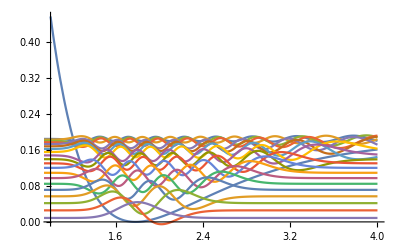

```mathematica
eigenPlot=Show[Plot[potentialFun[x],{x,1,L/2},PlotRange->Full],Plot[ Evaluate[0.02*eigxp+Energy],{x,0,L/2}]]
```

```mathematica
potentialEnergy=Table[NIntegrate[eigxp[[m]]* potentialFun[x]*eigxp[[m]],{x,0,L}],{m,1,20}]
```

{0.172056,0.1638,0.154948,0.146094,0.13724,0.128385,0.119531,0.110677,0.101823,0.0929687,0.0841146,0.0752604,0.0664062,0.0575521,0.0486979,0.0398437,0.0309896,0.0221354,0.0132812,0.00442708}

{0.0121338,0.0187721,0.0251712,0.0307249,0.035431,0.0392897,0.0423008,0.0444644,0.0457805,0.0462491,0.0458702,0.0446437,0.0425697,0.0396482,0.0358791,0.0312626,0.0257985,0.0194869,0.0123278,0.00432114}

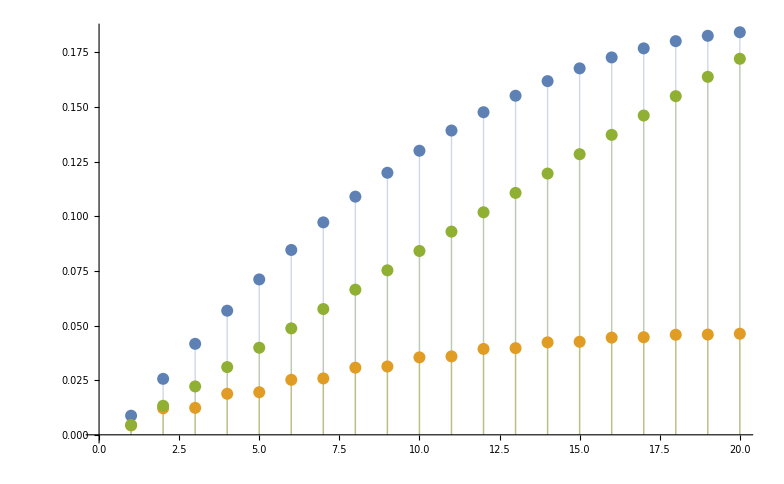

```mathematica
kineticEnergy=Table[Energy[[m]]-potentialEnergy[[m]],{m,1,20}]
Evaluate[ListPlot[{Sort[Energy],Sort[kineticEnergy],Sort[potentialEnergy]},Filling->Axis]]
```

```mathematica
β=1052.5822
averX=Table[NIntegrate[eigxp[[m]] x eigxp[[m]],{x,0,L}],{m,1,20}]

ΔX=Table[Sqrt[NIntegrate[eigxp[[m]] x^2eigxp[[m]],{x,0,L}]-averX[[m]]^2],{m,1,20}]
averP=Table[NIntegrate[eigxp[[m]] (-ⅈ *1728.16) *D[eigxp[[m]],x],{x,-L/2,L/2}],{m,1,20}]
ΔP=Table[Sqrt[NIntegrate[eigxp[[m]] *2*kineticEnerOperator[eigxp[[m]],x],{x,0,L}]-averP[[m]]^2],{m,1,20}]
```

1052.58

{5.67459,4.88283,4.338,3.94341,3.63601,3.38547,3.17487,2.99381,2.83545,2.69505,2.56919,2.45533,2.35152,2.25626,2.16833,2.08676,2.01077,1.93968,1.87295,1.81012}

{1.31465,1.21686,1.13022,1.05569,0.988658,0.926886,0.869039,0.814189,0.761634,0.710797,0.661171,0.612277,0.563625,0.514677,0.464776,0.413047,0.358181,0.297918,0.227418,0.130176}

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {1.74988}. NIntegrate obtained 0.-5.32907×10^-14 ⅈ and 4.75858×10^-11 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {1.81238}. NIntegrate obtained 0.+5.68434×10^-14 ⅈ and 7.29895×10^-11 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {1.703}. NIntegrate obtained 0.+5.68434×10^-14 ⅈ and 1.04491×10^-10 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{0.-5.32907×10^-14 ⅈ,0.+5.68434×10^-14 ⅈ,0.+5.68434×10^-14 ⅈ,0.-1.13687×10^-13 ⅈ,0.+7.2653×10^-13 ⅈ,0.+6.25278×10^-13 ⅈ,0.-6.25278×10^-13 ⅈ,0.-7.95808×10^-13 ⅈ,0.-5.6799×10^-13 ⅈ,0.+5.12035×10^-13 ⅈ,0.+1.7053×10^-13 ⅈ,0.-2.84217×10^-13 ⅈ,0.+6.28775×10^-13 ⅈ,0.-8.52651×10^-13 ⅈ,0.-6.25486×10^-13 ⅈ,0.+1.19371×10^-12 ⅈ,0.+6.82121×10^-13 ⅈ,0.-4.26326×10^-13 ⅈ,0.+5.11591×10^-13 ⅈ,0.+3.97904×10^-13 ⅈ}

{0.155781+0. ⅈ,0.193763+0. ⅈ,0.224371+0. ⅈ,0.247891+0. ⅈ,0.266199+0. ⅈ,0.28032+0. ⅈ,0.290864+0. ⅈ,0.298209+0. ⅈ,0.302591+0. ⅈ,0.304135+0. ⅈ,0.302887+0. ⅈ,0.29881+0. ⅈ,0.291787+0. ⅈ,0.281596+0. ⅈ,0.267877+0. ⅈ,0.25005+0. ⅈ,0.22715+0. ⅈ,0.197418+0. ⅈ,0.157021+0. ⅈ,0.0929639+0. ⅈ}

0.000100212

16210.8

84.7914 k

9978.86 (3.47339×10^-84 (0.154167 Sin[(π x)/8]-0.190807 Sin[(π x)/4]+0.132404 Sin[(3 π x)/8]+168+1.13702×10^-8 Sin[(117 π x)/8]-7.02888×10^-9 Sin[(59 π x)/4]-1.52846×10^-8 Sin[(119 π x)/8]-1.56104×10^-8 Sin[15 π x])^2+1.1668×10^-79 (-0.127288 Sin[(π x)/8]+0.0756846 Sin[1/4]+175)^2+2.24179×10^-77 (1)^2+14+6.3239×10^-85 1^2+1.48192×10^-81 (-0.151252 Sin[(π x)/8]+175+1.61547×10^-8 1)^2+4.59285×10^-83 (181+1.70725×10^-8 Sin[(119 π x)/8]+1.66641×10^-8 Sin[15 π x])^2)
 |  |  |  |

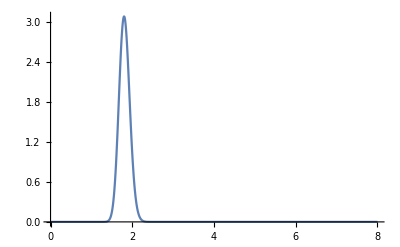

```mathematica
partitionFunc=Sum[Exp[-β Energy[[m]]],{m,1,20}]
EnsembleEnergy=Sum[Exp[-β Energy[[m]] Energy[[m]]]/partitionFunc,{m,1,20}]
heatCap=Sum[Quantity["BoltzmannConstant"] β^2  Energy[[m]]^2 Exp[-β Energy[[m]]],{m,1,20}]/partitionFunc
canonicalDistri=Sum[Exp[-β Energy[[m]] ]*eigxp[[m]]* eigxp[[m]],{m,1,20}]/partitionFunc
Evaluate[Plot[canonicalDistri,{x,0,L},PlotRange->Full]]
```

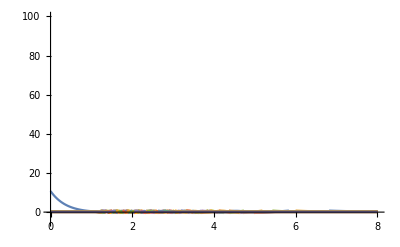

EigenFunction.jpg

Energy.txt

EnergyPlot.jpg

X_Fluctuation.txt

P_Fluctuation.txt

26201.2

22575.1

EnsembleEnergy.txt

HeatCapacity.txt

CanonicalLocationDistribution.jpg

```mathematica
Show[Plot[potentialFun[x],{x,0,L},PlotRange->{-5,100}],Plot[ Evaluate[eigxp+Energy],{x,0,L}]]
Export["EigenFunction.jpg",eigenPlot]
Export["Energy.txt",{Reverse[Energy],Reverse[kineticEnergy],Reverse[potentialEnergy]}]
Export["EnergyPlot.jpg",Evaluate[ListPlot[{Reverse[Energy],Reverse[kineticEnergy],Reverse[potentialEnergy]},Filling->Axis]]]
Export["X_Fluctuation.txt",Reverse[ΔX]]
Export["P_Fluctuation.txt",Reverse[ΔP]]
EnsembleKinetic=Sum[Exp[-β Energy[[m]] kineticEnergy[[m]]]/partitionFunc,{m,1,20}]
EnsemblePotential=Sum[Exp[-β Energy[[m]] potentialEnergy[[m]]]/partitionFunc,{m,1,20}]
Export["EnsembleEnergy.txt",{EnsembleEnergy,EnsembleKinetic,EnsemblePotential}]
Export["HeatCapacity.txt",heatCap]
Export["CanonicalLocationDistribution.jpg",Evaluate[Plot[canonicalDistri,{x,0,L},PlotRange->Full]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["CanonicalLocationDistribution.jpg"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["CanonicalLocationDistribution.jpg"]]]
```

```mathematica
ScientificForm[partitionFunc]
```

1.00212×10^-4

Part::pkspec1: The expression  cannot be used as a part specification.